```mathematica
(*--------------------quasicrystal--------------------------*)
```

```mathematica
Lx=7;
Ly=7;
```

```mathematica
NOrbitals=2*Lx*Ly;
```

```mathematica
Clear[Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,NOrbitals,2}];
```

```mathematica
(**--Equations for the two red lines--**)
```

```mathematica
LineUp[x_]:=((1+√5)/2)^-1*(x-1)+2.5
LineDn[x_]:=((1+√5)/2)^-1*(x-2)+1.6
```

```mathematica
l1=4;m=4;
```

```mathematica
SitesRemoved={}
```

{}

```mathematica
Do[SitesRemoved=Append[SitesRemoved,{m,y}],{y,1,l1-1}]
```

```mathematica
Sites = Complement[Sites,SitesRemoved];
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[Fibonup,Fibondown,TotalFibon,XList, YList]
```

```mathematica
(**-----We want to count points inside the area of interest, store them in FibonupNew, and sort them into Fibonup-----**)
```

```mathematica
Clear[FibonupNew]
FibonupNew={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
Do[Do[FibonupNew=Append[FibonupNew,x+(y-1)*Lx],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx}]
```

```mathematica
FibonupNew;
```

```mathematica
Fibonlist=Sort[FibonupNew]
```

{1,8,9,16,17,18,25,26,34,35,42}

```mathematica
NSitesQuasi = Dimensions[Fibonlist][[1]];
```

```mathematica
YList = Ceiling[Fibonlist/Lx]
```

{1,2,2,3,3,3,4,4,5,5,6}

```mathematica
XList = Fibonlist - (YList - 1)Lx
```

{1,1,2,2,3,4,4,5,6,7,7}

```mathematica
(**Check that the list is correct**)
```

```mathematica
XList + (YList-1)*Lx - Fibonlist
```

{0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ListOfActualPointsInQuasi=Complement[Table[{XList[[k]],YList[[k]]},{k,1,NSitesQuasi}],SitesRemoved]
```

{{1,1},{1,2},{2,2},{2,3},{3,3},{4,4},{5,4},{6,5},{7,5},{7,6}}

```mathematica
(**--Compare with the previous (manually calculated) Fibonup for 20x20 sites--**)
```

```mathematica
(**--Fibonup={1,22,23,43,44,45,65,66,86,87,88,108,109,110,130,131,151,152,153,173,174,194,195,196,216,217,218,238,239,259,260};--**)
```

```mathematica
(** Now we find the equations of lines **)
```

```mathematica
Clear[xx,yy,x,y]
```

```mathematica
xx={};
yy={};
```

```mathematica
Do[{s=Solve[y==LineDn[x]&& (y-ListOfActualPointsInQuasi[[k]][[2]])/(x-ListOfActualPointsInQuasi[[k]][[1]])==-((1+√5)/2) ,{x,y}],xx = Append[xx,s[[All,1,2]]],yy = Append[yy,s[[All,2,2]]]},{k,1,NSitesQuasi}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Part::partw: Part 11 of {{1,1},{1,2},{2,2},{2,3},{3,3},{4,4},{5,4},{6,5},{7,5},{7,6}} does not exist.

```mathematica
xx;
```

```mathematica
yy;
```

```mathematica
ListOfQuasiPoints=Table[{xx[[k,1]],yy[[k,1]]},{k,1,NSitesQuasi}];
```

Part::partw: Part 1 of {} does not exist.

```mathematica
ListofPointsOutSide = Complement[Sites,ListOfActualPointsInQuasi];
```

```mathematica
ListofPointsOutSideUp
```

{{1,3},{1,4},{1,5},{1,6},{1,7},{2,4},{2,5},{2,6},{2,7},{3,4},{3,5},{3,6},{3,7},{4,5},{4,6},{4,7},{5,5},{5,6},{5,7},{6,6},{6,7},{7,7}}

```mathematica
{ListofPointsOutSideDn={},Do[If[LineUp[ListofPointsOutSide[[ii]][[1]]]>  ListofPointsOutSide[[ii]][[2]],ListofPointsOutSideDn=Append[ListofPointsOutSideDn,ListofPointsOutSide[[ii]]]],{ii,1,Dimensions[ListofPointsOutSide][[1]]}]}
```

{{},Null}

```mathematica
ListofPointsOutSideUp = Complement[ListofPointsOutSide,ListofPointsOutSideDn];
```

```mathematica
YList[[5]]
```

3

```mathematica
ListOfActualPointsInQuasi[[5]][[2]]
```

3

```mathematica
(** First and the last points are omitted **)
```

```mathematica
A=Table[Plot[ListOfActualPointsInQuasi[[k]][[2]]-((1+√5)/2)*((x-ListOfActualPointsInQuasi[[k]][[1]])),{x,ListOfActualPointsInQuasi[[k]][[1]],xx[[k,1]]},PlotStyle->{Dashed,Black}],{k,2,NSitesQuasi-2}];
```

```mathematica
(** {H11={},Do[{xxxx=Solve[LineDn[x]==yyyy][[All,1,2]][[1]],H11=Append[H11,Plot[yyyy,{x,Max[1,Ceiling[xxxx]],Lx}]]},{yyyy,1,Floor[LineDn[Lx]]}],
Do[{xxxx=Solve[LineUp[x]==yyyy][[All,1,2]][[1]],H11=Append[H11,Plot[yyyy,{x,1,Min[Floor[xxxx],Lx]}]]},{yyyy,Ceiling[LineUp[1]],Ly}]}; **)
```

```mathematica
Clear[H11]
```

```mathematica
{H11={},Do[Do[If[Norm[ListofPointsOutSideDn[[ii]]-ListofPointsOutSideDn[[jj]]]==1,H11=Append[H11,Graphics[{Black,Line[{ListofPointsOutSideDn[[ii]],ListofPointsOutSideDn[[jj]]}]}]],0],{ii,1,Dimensions[ListofPointsOutSideDn][[1]]}],{jj,1,Dimensions[ListofPointsOutSideDn][[1]]}]}
```

{{},Null}

```mathematica
Do[Do[If[Norm[ListofPointsOutSideDn[[ii]]-ListofPointsOutSideDn[[jj]]]==2,H11=Append[H11,Graphics[{Black,Line[{ListofPointsOutSideDn[[ii]],ListofPointsOutSideDn[[jj]]}]}]],0],{ii,1,Dimensions[ListofPointsOutSideDn][[1]]}],{jj,1,Dimensions[ListofPointsOutSideDn][[1]]}]
```

```mathematica
Do[Do[If[Norm[ListofPointsOutSideUp[[ii]]-ListofPointsOutSideUp[[jj]]]==1,H11=Append[H11,Graphics[{Black,Line[{ListofPointsOutSideUp[[ii]],ListofPointsOutSideUp[[jj]]}]}]],0],{ii,1,Dimensions[ListofPointsOutSideUp][[1]]}],{jj,1,Dimensions[ListofPointsOutSideUp][[1]]}]
```

```mathematica
Do[Do[If[Norm[ListofPointsOutSideUp[[ii]]-ListofPointsOutSideUp[[jj]]]==2,H11=Append[H11,Graphics[{Black,Line[{ListofPointsOutSideUp[[ii]],ListofPointsOutSideUp[[jj]]}]}]],0],{ii,1,Dimensions[ListofPointsOutSideUp][[1]]}],{jj,1,Dimensions[ListofPointsOutSideUp][[1]]}]
```

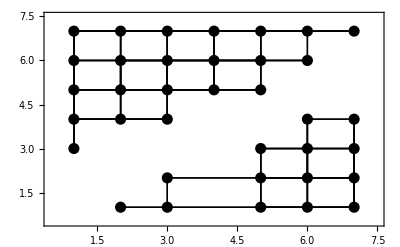

```mathematica
Show[ListPlot[ListofPointsOutSideUp,PlotStyle-> {Black,PointSize[0.02]}],
ListPlot[ListofPointsOutSideDn,PlotStyle-> {Black,PointSize[0.02]}],
H11,Frame-> True,Axes-> False,PlotRange-> {{0.5,Lx+0.5},{0.5,Ly+0.5}}]
```

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.02]}],H11,Frame-> True,Axes-> False,PlotRange-> {{0.5,Lx+0.5},{0.5,Ly+0.5}}];
```

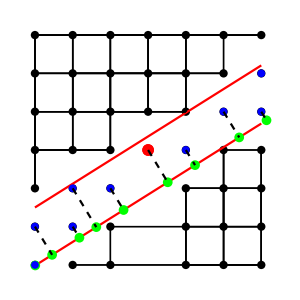

```mathematica
B=Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.02]},Axes-> False,PlotRange-> {{0.8,Lx+0.3},{0.8,Ly+0.2}}],
Plot[LineUp[x],{x,1,Lx},PlotStyle-> Red],
Plot[LineDn[x],{x,1,Lx},PlotStyle-> Red],
ListPlot[ListOfQuasiPoints, PlotStyle->Green,PlotMarkers->{Automatic,10}],
ListPlot[ListOfActualPointsInQuasi, PlotStyle->Blue,PlotMarkers->{Automatic,8}],
ListPlot[{{m,l1}}, PlotStyle->Red,PlotMarkers->{Automatic,12}],
A,H11,
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
FrameTicks-> {{None,None},{None,None}},
ImageSize-> 300,AspectRatio-> 1
]
```

```mathematica
(** Do[Do[If[Norm[ListOfActualPointsInQuasi[[ii]]-ListOfActualPointsInQuasi[[jj]]]==1,H22=Append[H22,Graphics[{Yellow,Line[{{ListOfActualPointsInQuasi[[ii]]},{ListOfActualPointsInQuasi[[jj]]}}]}]],0],{ii,1,Dimensions[ListOfActualPointsInQuasi][[1]]}],{jj,1,Dimensions[ListOfActualPointsInQuasi][[1]]}] **)
```

```mathematica
Clear[H12, H22]
```

```mathematica
{H22={},Do[Do[If[Norm[ListOfActualPointsInQuasi[[ii]]-ListOfActualPointsInQuasi[[jj]]]==1,H22=Append[H22,Graphics[{Blue,Line[{ListOfActualPointsInQuasi[[ii]],ListOfActualPointsInQuasi[[jj]]}]}]],0],{ii,1,Dimensions[ListOfActualPointsInQuasi][[1]]}],{jj,1,Dimensions[ListOfActualPointsInQuasi][[1]]}]}
```

{{},Null}

```mathematica
H22;
```

```mathematica
{H12={},Do[Do[If[Norm[ListOfActualPointsInQuasi[[ii]]-ListofPointsOutSide[[jj]]]==1,H12=Append[H12,Graphics[{Purple,Dotted,Thick,Line[{ListOfActualPointsInQuasi[[ii]],ListofPointsOutSide[[jj]]}]}]],0],{ii,1,Dimensions[ListOfActualPointsInQuasi][[1]]}],{jj,1,Dimensions[ListofPointsOutSide][[1]]}]}
```

{{},Null}

```mathematica
(** Just for a special case **)
```

```mathematica
H12=Append[H12,Graphics[{Purple,Dotted,Thick,Line[{{3,3},{5,3}}]}]];
```

```mathematica
Show[H12];
```

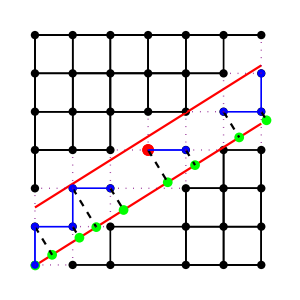

```mathematica
Show[B,H22,H12]
```